Maxime Beau & Arnd Roth 29.11.16

```mathematica
SetDirectory["/Users/roth/Documents/Arnd/Circuit Reconstruction/Maxime"]
```

/Users/roth/Documents/Arnd/Circuit Reconstruction/Maxime

## Original connectivity

```mathematica
dataBefore=ToExpression[Import["before.txt"]];
```

```mathematica
mytimes=Range[0.,4.95,0.025];
```

```mathematica
dataBefore=Drop[dataBefore,33];
mytimes=Drop[mytimes,-33];
```

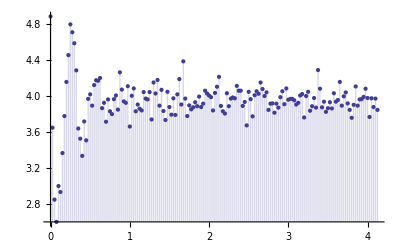

```mathematica
dataPlotBefore=ListPlot[Transpose[{mytimes,dataBefore}],Filling->Axis,PlotRange->All]
```

```mathematica
fitResultBefore=FindFit[Transpose[{mytimes,dataBefore}],baseline+Exp[-gamma t] a Cos[omega1 t-alpha],{baseline,gamma,a,omega1,alpha},t]
```

{baseline→3.95256,gamma→3.63718,a→-1.91324,omega1→19.5401,alpha→8.23668}

```mathematica
rate[t_]:=baseline+Exp[-gamma t] a Cos[omega1 t-alpha]
```

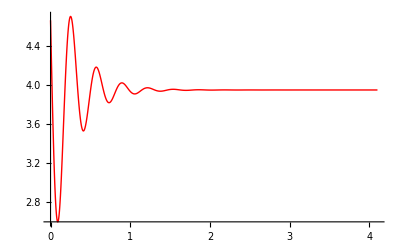

```mathematica
fitPlotBefore=Plot[rate[t]/.fitResultBefore,{t,0,4.1},PlotStyle->Hue[0.],PlotRange->All]
```

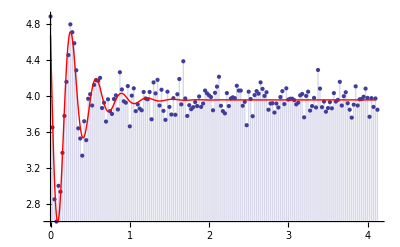

```mathematica
Show[dataPlotBefore,fitPlotBefore]
```

## Transformed connectivity

```mathematica
dataAfter=ToExpression[Import["after.txt"]];
```

```mathematica
mytimes=Range[0.,4.95,0.025];
```

```mathematica
dataAfter=Drop[dataAfter,33];
mytimes=Drop[mytimes,-33];
```

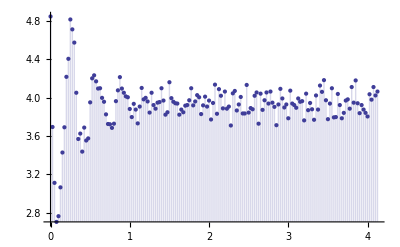

```mathematica
dataPlotAfter=ListPlot[Transpose[{mytimes,dataAfter}],Filling->Axis,PlotRange->All]
```

```mathematica
fitResultAfter=FindFit[Transpose[{mytimes,dataAfter}],baseline+Exp[-gamma t] a Cos[omega1 t-alpha],{baseline,gamma,a,omega1,alpha},t]
```

{baseline→3.94193,gamma→2.93918,a→1.66943,omega1→19.7136,alpha→5.14087}

gamma is smaller -> the oscillation decays more slowly

```mathematica
rate[t_]:=baseline+Exp[-gamma t] a Cos[omega1 t-alpha]
```

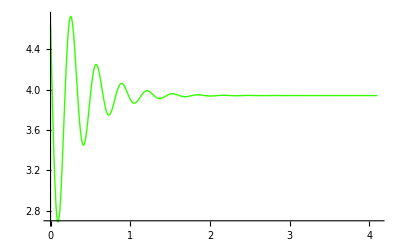

```mathematica
fitPlotAfter=Plot[rate[t]/.fitResultAfter,{t,0,4.1},PlotStyle->Hue[0.3],PlotRange->All]
```

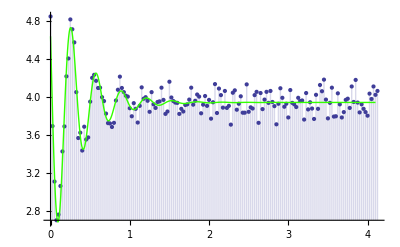

```mathematica
Show[dataPlotAfter,fitPlotAfter]
```

## Comparison of the fits

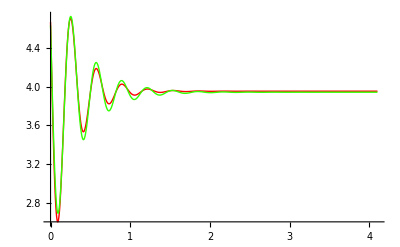

```mathematica
Show[fitPlotBefore, fitPlotAfter]
```